## June 25, 2019

### Art of Project Development (Important Notes)

#### Think functionally

Use immutable data

Wolfram data is by default immutable

Helpful for asynchronous programming

Don’t rely on global state

Immutable data are thread safe

Use map and functional constructs instead of imperative constructs

#### Think, design and fail

Before coding think at the outcome

Split your project in components, write down responsibility, write down a pipeline, try to anticipate possible problems and outcomes

Failure is not your enemy

#### Principles and Concepts

Expressions

```mathematica
Quantity[32.82, "USDollars"]
```

```mathematica
Quantity["32.82", "USDollars"]
```

Head and Body

```mathematica
f[x]
```

f[x]

Body may be empty

```mathematica
f[]
```

f[]

Compound Atomic Expressions

Graph

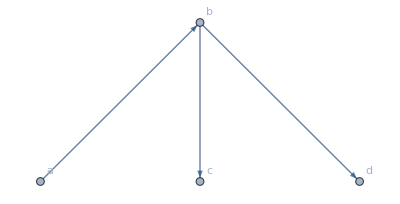

```mathematica
g=Graph[{a->b, b->c, b->d}, VertexLabels->Automatic]
```

Notation Style

FullForm

```mathematica
Plus[2, Times[3,x]]
```

2+3 x

```mathematica
%//FullForm
```

Plus[2,Times[3,x]]

```mathematica
q= 3;
r=4;
s=2;
q^(r-s);
```

Postfix

```mathematica
Map[Cos, {1,2,3}] // Mod[#,3]&
```

{Cos[1],3+Cos[2],3+Cos[3]}

```mathematica
x= RandomInteger[{0,10}, {5,3}] // Grid
```

```mathematica
{{8, 4, 7}, {9, 4, 1}, {2, 3, 5}, {5, 0, 2}, {10, 2, 5}}
```

#### Training for Programmers

Symbols

```mathematica
MatrixForm[{{1,2},{3,4},{5,6}}]
```

(1 | 2
3 | 4
5 | 6)

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
y = Plus[Times[3,Power[x,2]], Times[2,x],4]
```

4+2 x+3 x^2

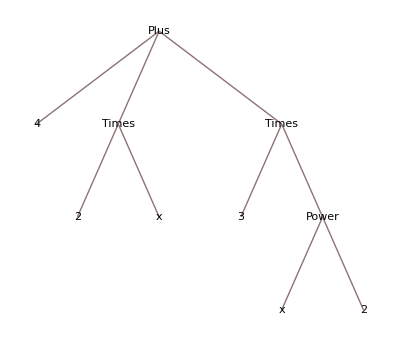

```mathematica
4+2 x+3 x^2
TreeForm[%]
```

```mathematica
Head[x]
```

Symbol

Head of objects themselves are symbols

```mathematica
SymbolName[x]
```

x

```mathematica
Names["Global`*"]
```

{a,b,c,d,expr,f,g,i,Matrix,opts,pi,q,r,s,sol,system,t,t$,uspec,x,X,x$,y}

Pure Functions

```mathematica
Clear[x]
```

```mathematica
Function[# / 2][x]
```

x/2

```mathematica
Function[#1 / 2+ #2][x, 4]
```

4+x/2

```mathematica
Function[{arg1, arg2}, arg1/ 2 + arg2][x,4]
```

4+x/2